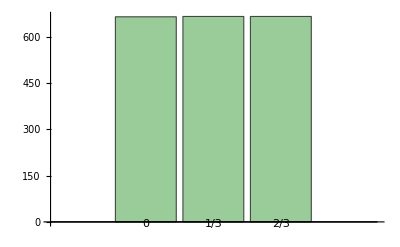

```mathematica
r=8/3;
rseq=Table[Mod[i*r,1],{i,1,2000,1}];
BarChart[Labeled@@@Reverse[Sort[Tally[rseq]],2],ChartStyle->RGBColor["#99cc99"]]
```

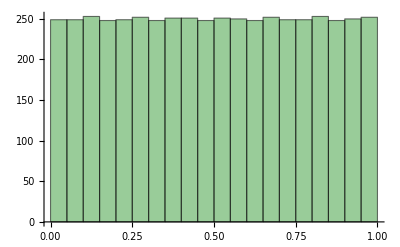

```mathematica
(*Dense and uniformly distributed*)
ir=100 Sqrt[2];
irseq=Table[N[Mod[i*ir,1]],{i,1,5000,1}];
Histogram[irseq,ChartStyle->RGBColor["#99cc99"]]
BarChart[Labeled@@@Reverse[Sort[Tally[irseq]],2]];
```

```mathematica
(*Dense not uniformly distributed*)
lseq=Table[N[Mod[Log[i],1]],{i,1,5000,1}];
Histogram[lseq,ChartStyle->RGBColor["#99cc99"]]
BarChart[Labeled@@@Reverse[Sort[Tally[lseq]],2]];
```